Moments and Cumulants of  A

```mathematica
m1A = M * m1R^2;
m2A = M*(M-1) m1R^4 + M*m2R^2;
m3A = M*(M-1)*(M-2) * m1R^6 + 3 M (M-1) m2R^2 m1R^2 + M m3R^2;
m4A = M*m4R^2 + 4 M (M-1) m3R^2 m1R^2 + 6 M (M-1) (M-2) m2R^2 m1R^4 + 3 M (M-1) m2R^4 + M (M-1) (M-2) (M-3) m1R^8;


k1A = m1A;
k2A = m2A - m1A^2;
k3A = m3A  - 3 m2A m1A + 2 m1A^3;
k4A = m4A - 4 m3A m1A - 3 m2A^2 +12 m2A m1A^2 -6 m1A^4;
skewComp = k3A/k2A^(3/2);
kurtosisComp = k4A / k2A^2 - 3;

paramAssumption = {m1R>0,m2R>0,m3R>0,M>0,m1D>0,m2D>0,m3D>0,l>0,Element[m1R,Reals],Element[m2R,Reals],Element[m3R,Reals],Element[M,Reals],Element[m1D,Reals],Element[m2D,Reals],Element[m3D,Reals],Element[l,Reals]};
scalingAssumption = {m1D->1/(M-1),m2D->1/(M-1)^2,m3D->1/(M-1)^3};

FullSimplify[k1A,Assumptions->paramAssumption]
FullSimplify[k2A,Assumptions->paramAssumption]
FullSimplify[k3A,Assumptions->paramAssumption]
FullSimplify[k4A,Assumptions->paramAssumption]
FullSimplify[skewComp,Assumptions->paramAssumption]
FullSimplify[kurtosisComp,Assumptions->paramAssumption]
```

M m1R^2

M (-m1R^4+m2R^2)

M (2 m1R^6-3 m1R^2 m2R^2+m3R^2)

M (-6 m1R^8+12 m1R^4 m2R^2-3 m2R^4-4 m1R^2 m3R^2+m4R^2)

(-2 m1R^6+3 m1R^2 m2R^2-m3R^2)/((m1R^4-m2R^2) √(M (-m1R^4+m2R^2)))

(-3 (2+M) m1R^8+6 (2+M) m1R^4 m2R^2-3 (1+M) m2R^4-4 m1R^2 m3R^2+m4R^2)/(M (m1R^4-m2R^2)^2)

Moments  of  B

```mathematica
m1B = m1R^2 m1D M (M-1);
m2B = M (M-1) m2R^2 m2D + 2 M (M-1) (M-2) m2R m1R^2 m1D^2 + M (M-1) (M-2) (M-3) m1R^4 m1D^2;

k1B = m1B;
k2B = m2B - m1B^2;
m1AB = M (M-1) (M-3) m1R^4 m1D + 2 M (M-1) m2R m1R^2 m1D;
m1A2B = 2 M (M-1) m3R m2R m1R m1D + 2 M (M-1) m2R^2 m1R^2 m1D + 4 M (M-1) (M-2) m2R m1R^4 m1D + M (M-1) (M-2) (M-3) m1R^6 m1D;
covAB = m1AB - m1A m1B;
covA2A = m3A - m2A * m1A;
covABA = m1A2B - m1AB m1A;
```

```mathematica
k1cross = m1A - l*(m1A + m1B);
k2cross = k2A - 2 l (k2A + covAB);
k3cross = k3A -3 l (k3A + covABA - m1B k2A - m1A k2B);
skewCross = k3cross/k2cross^(3/2);

Collect[FullSimplify[k1cross/.scalingAssumption,Assumptions->paramAssumption],l]
Collect[FullSimplify[k2cross/.scalingAssumption,Assumptions->paramAssumption],l]
Collect[FullSimplify[k3cross/.scalingAssumption,Assumptions->paramAssumption],l]
orderlskew = Collect[FullSimplify[skewCross/.scalingAssumption,Assumptions->paramAssumption],l]
```

M m1R^2-2 l M m1R^2

M (-m1R^2-m2R) (m1R^2-m2R)+l M (m1R^2-m2R) (6 m1R^2+2 m2R)

(l M (-6 (-4+M (2+M)) m1R^6+6 (-4+3 M) m1R^4 m2R+3 (-1+M+M^2) m1R^2 m2R^2-6 (-1+M) m1R m2R m3R-3 (-1+M) m3R^2))/(-1+M)+(M (-2 m1R^6+2 M m1R^6+3 m1R^2 m2R^2-3 M m1R^2 m2R^2-m3R^2+M m3R^2))/(-1+M)

(l M (-6 (-4+M (2+M)) m1R^6+6 (-4+3 M) m1R^4 m2R+3 (-1+M+M^2) m1R^2 m2R^2-6 (-1+M) m1R m2R m3R-3 (-1+M) m3R^2))/((-1+M) (M (m1R^2-m2R) ((-1+6 l) m1R^2+(-1+2 l) m2R))^(3/2))+(M (-2 m1R^6+2 M m1R^6+3 m1R^2 m2R^2-3 M m1R^2 m2R^2-m3R^2+M m3R^2))/((-1+M) (M (m1R^2-m2R) ((-1+6 l) m1R^2+(-1+2 l) m2R))^(3/2))

```mathematica
paramValues = {m1R -> 1/M ,m2R->(1+x^2)/M^2,m3R->(1+x^2)^3/M^3,m4R->(1+x^2)^6/M^4}
```

{m1R→1/M,m2R→(1+x^2)/M^2,m3R→((1+x^2)^3)/M^3,m4R→((1+x^2)^6)/M^4}

```mathematica
acrossLskewCross = orderlskew/.paramValues //Simplify
```

-(-((-1+M) x^4 (2+x^2)^2 (3+2 x^2+x^4))-3 l (2+4 x^2+26 x^4+28 x^6+17 x^8+6 x^10+x^12+M^2 (-1+2 x^2+x^4)-M x^2 (6+26 x^2+28 x^4+17 x^6+6 x^8+x^10)))/((-1+M) M^5 ((x^2 (2+x^2-2 l (4+x^2)))/M^3)^(3/2))

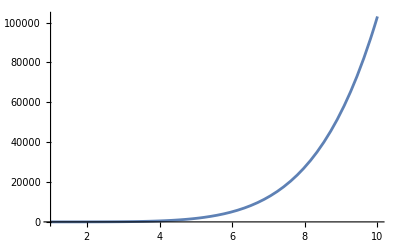

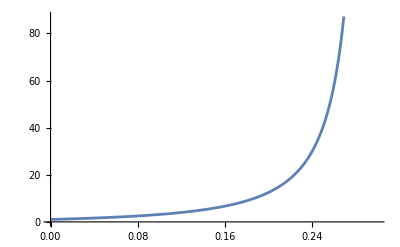

```mathematica
Plot[acrossLskewCross/.{M->100,l->0},{x,1,10}]
Plot[acrossLskewCross/.{M->100,x->1},{l,0,0.3}]
```

```mathematica
momentRatioA = FullSimplify[(m1A * m3A / m2A^2)/.scalingAssumption,Assumptions->paramAssumption];
cumulantRatioA = FullSimplify[(k1A * k3A / k2A^2)/.scalingAssumption,Assumptions->paramAssumption];
```

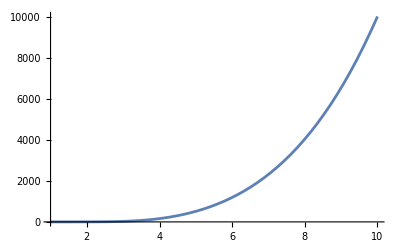

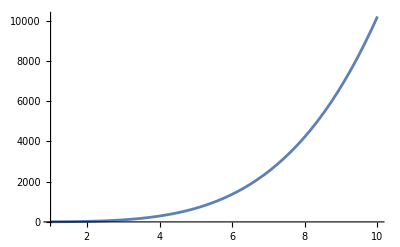

```mathematica
Plot[(momentRatioA/.paramValues)/.M->100,{x,1,10}]
Plot[(cumulantRatioA/.paramValues)/.M->100,{x,1,10}]
```

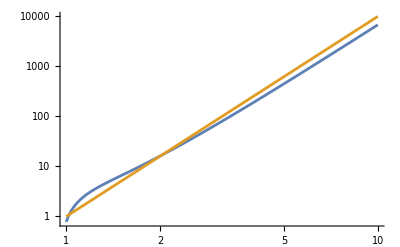

```mathematica
pearsonRatio = ((2*kurtosisComp / (3 * skewComp^2))/.paramValues)/.(M->100) //FullSimplify;
LogLogPlot[{pearsonRatio,x^4},{x,1,10}]
```

```mathematica
simplifiedSkew=(skewComp/.paramValues)/.M->100 //FullSimplify
simplifiedKurtosis = (kurtosisComp/.paramValues)/.M->100 //FullSimplify
```

1/10 √(x^2 (2+x^2)) (3+2 x^2+x^4)

-3+1/100 x^2 (2+x^2) (16+x^2 (2+x^2) (15+x^2 (2+x^2) (6+2 x^2+x^4)))

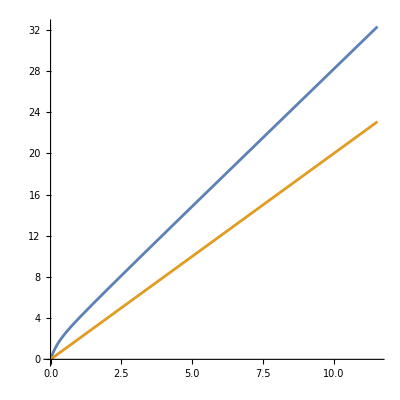

```mathematica
ParametricPlot[{{Log[simplifiedSkew],Log[simplifiedKurtosis]},{Log[simplifiedSkew],2*Log[simplifiedSkew]}},{x,1,10},AspectRatio->1]
```